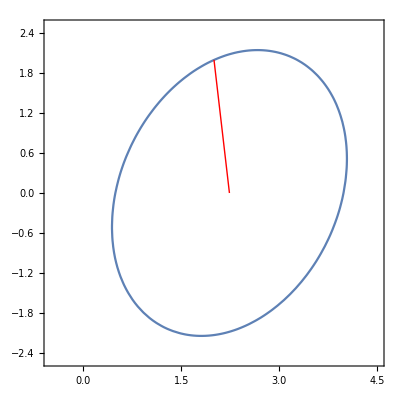

{1,7}

{2.23607,0}

```mathematica
F1[x_,y_]:=10 x^2-4x y+7 y^2-4 √5(5x-y)-16;
F2[x_,y_]:=(x^2-y)^2+(x-1)^2;
F3[x_,y_]:=5*(x^2-y)^2+(x-1)^2;
str=Import["D:/1/MOVI lab/labor4/lab4/Newtoneps1f1p1.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,-0.5,4.5},{y,-2.5,2.5},MaxRecursion->3],{i,2,Length[str]-1}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
```

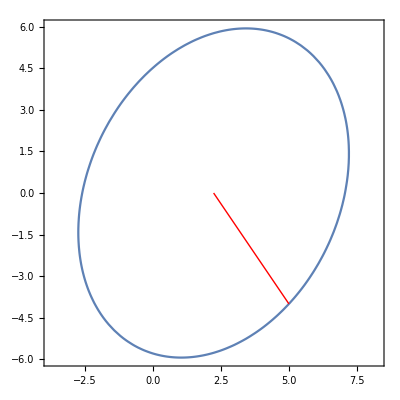

{1,7}

{2.23607,0}

```mathematica
str=Import["D:/1/MOVI lab/labor4/lab4/Newtoneps1f1p2.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,-3.75,8.25},{y,-6,6},MaxRecursion->3],{i,2,Length[str]-1}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
```

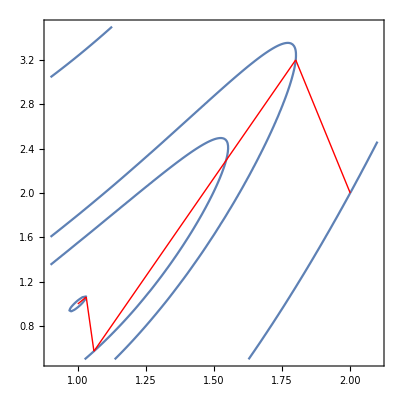

{4,22}

{1.00005,0.999141}

```mathematica
str=Import["D:/1/MOVI lab/labor4/lab4/Newtoneps1f2p1.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,0.9,2.1},{y,0.5,3.5},MaxRecursion->3],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
```

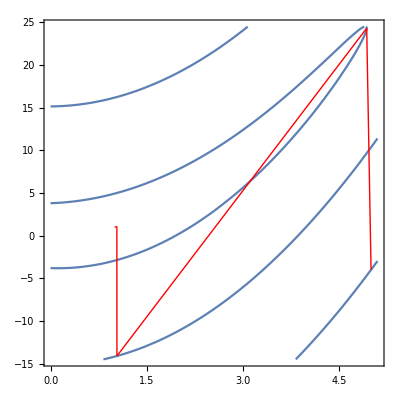

{4,22}

{1,0.998798}

```mathematica
str=Import["D:/1/MOVI lab/labor4/lab4/Newtoneps1f2p2.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,0,5.1},{y,-14.5,24.5},MaxRecursion->3],{i,2,Length[str]-1}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
```

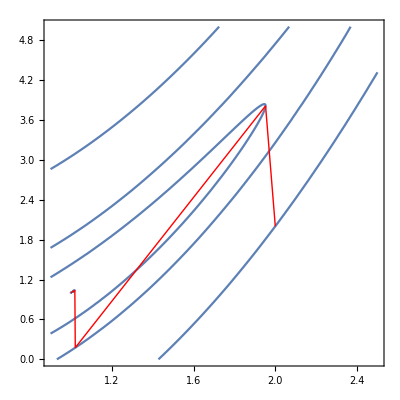

{4,22}

{1.,0.999643}

```mathematica
str=Import["D:/1/MOVI lab/labor4/lab4/Newtoneps1f3p1.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,0.9,2.5},{y,0,5},MaxRecursion->3],{i,2,Length[str]-1}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
```

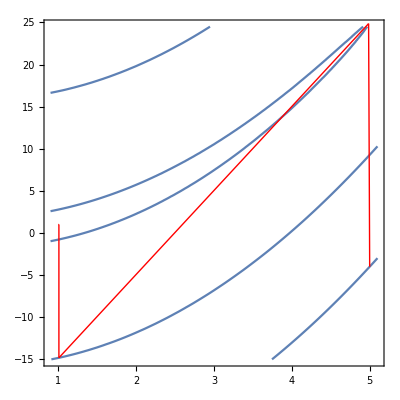

{4,22}

{1,0.999944}

```mathematica
str=Import["D:/1/MOVI lab/labor4/lab4/Newtoneps1f3p2.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,0.9,5.1},{y,-15,24.5},MaxRecursion->3],{i,2,Length[str]-1}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
```

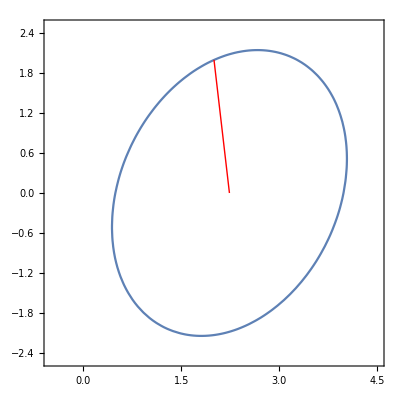

{1,31}

{2.23607,-0.0000108085}

```mathematica
str=Import["D:/1/MOVI lab/labor4/lab4/Newtonstepeps1f1p1.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,-0.5,4.5},{y,-2.5,2.5},MaxRecursion->3],{i,2,Length[str]-1}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
```

```mathematica
str=Import["D:/1/MOVI lab/labor4/lab4/Newtonstepeps1f1p2.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,-3.75,8.25},{y,-6,6},MaxRecursion->3],{i,2,Length[str]-1}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
```

-Graphics-

{1,29}

{2.23608,-0.0000129238}

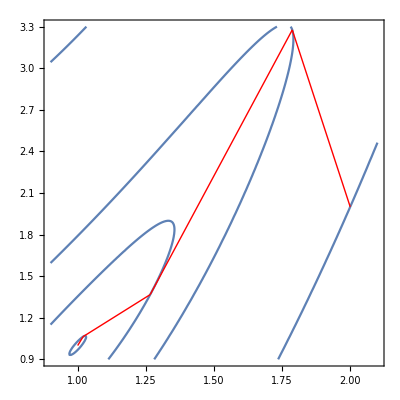

{4,135}

{0.999607,0.999538}

```mathematica
str=Import["D:/1/MOVI lab/labor4/lab4/Newtonstepeps1f2p1.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,0.9,2.1},{y,0.9,3.3},MaxRecursion->3],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
```

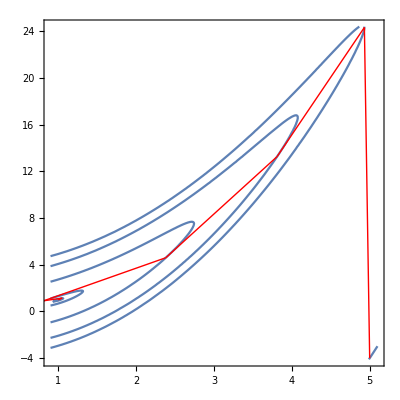

{6,204}

{0.999352,0.999427}

```mathematica
str=Import["D:/1/MOVI lab/labor4/lab4/Newtonstepeps1f2p2.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,0.9,5.1},{y,-4.1,24.4},MaxRecursion->3],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
```

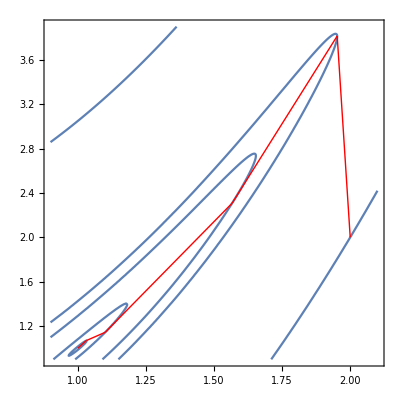

{6,176}

{1.,1.}

```mathematica
str=Import["D:/1/MOVI lab/labor4/lab4/Newtonstepeps1f3p1.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,0.9,2.1},{y,0.9,3.9},MaxRecursion->3],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
```

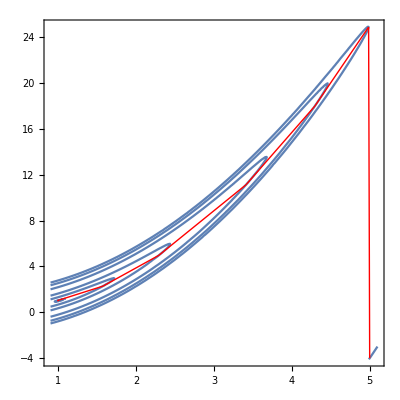

{7,205}

{1.00861,1.01808}

```mathematica
str=Import["D:/1/MOVI lab/labor4/lab4/Newtonstepeps1f3p2.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,0.9,5.1},{y,-4.1,24.9},MaxRecursion->3],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
```

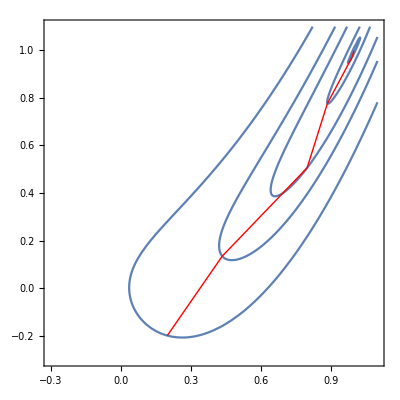

{5,27}

{0.999184,0.998317}

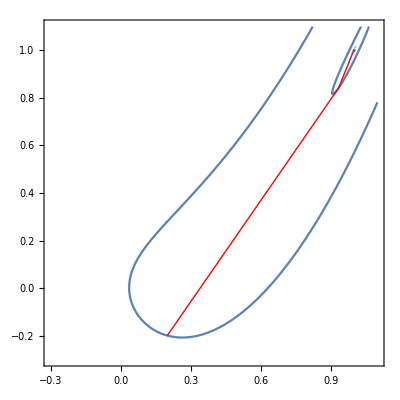

{3,92}

{1.00003,1.00006}

```mathematica
str=Import["D:/1/MOVI lab/labor4/lab4/Newtoneps1f3p3.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-0.3,1.1},{y,-0.3,1.1},MaxRecursion->3],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
str=Import["D:/1/MOVI lab/labor4/lab4/Newtonstepeps1f3p3.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-0.3,1.1},{y,-0.3,1.1},MaxRecursion->3],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
```

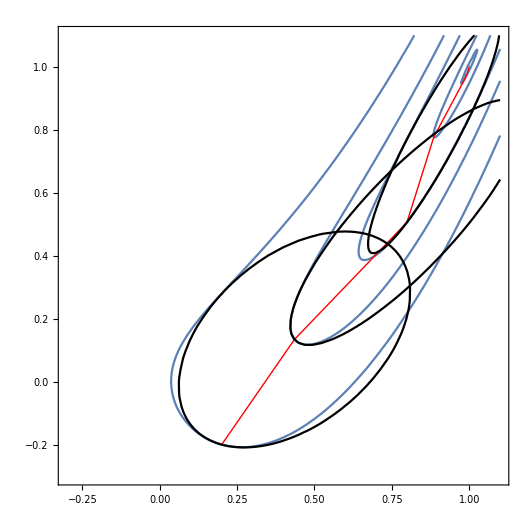

{5,27}

{0.999184,0.998317}

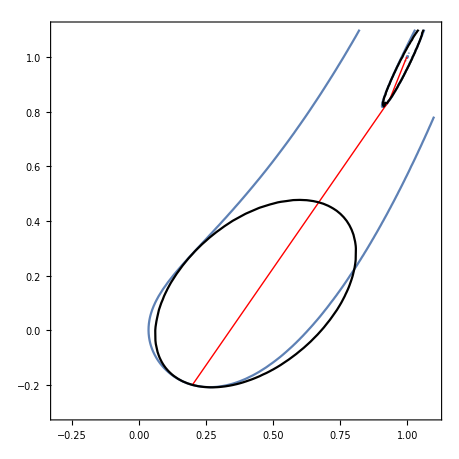

{3,92}

{1.00003,1.00006}

```mathematica
A={{D[D[F3[x,y],x],x],D[D[F3[x,y],x],y]},{D[D[F3[x,y],y],x],D[D[F3[x,y],y],y]}};
G={D[F3[x,y],x],D[F3[x,y],y]};
Ax=A/.{x->0.2,y->-0.2};Gx=G/.{x->0.2,y->-0.2};
str=Import["D:/1/MOVI lab/labor4/lab4/Newtoneps1f3p3.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-0.3,1.1},{y,-0.3,1.1},MaxRecursion->3],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Pf=Table[(G/.{x->str[[i,1]],y->str[[i,2]]}).({x,y}-str[[i]])+(1/2(A/.{x->str[[i,1]],y->str[[i,2]]}).({x,y}-str[[i]])).({x,y}-str[[i]]),{i,2,Length[str]}];
P=Table[ContourPlot[Pf[[i]]==0,{x,-0.3,1.1},{y,-0.3,1.1},ContourStyle->Black],{i,1,Length[str]-5}];

Show[K,M,P]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/labor4/lab4/Newtonstepeps1f3p3.txt","Table"];
Pf=Table[(G/.{x->str[[i,1]],y->str[[i,2]]}).({x,y}-str[[i]])+(1/2(A/.{x->str[[i,1]],y->str[[i,2]]}).({x,y}-str[[i]])).({x,y}-str[[i]]),{i,2,Length[str]}];
P=Table[ContourPlot[Pf[[i]]==0,{x,-0.3,1.1},{y,-0.3,1.1},ContourStyle->Black],{i,1,Length[str]-4}];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-0.3,1.1},{y,-0.3,1.1},MaxRecursion->3],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Thickness[Small],Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M,P]
str[[1]]
str[[Length[str]]]
```